John W. & Cassie H.     6/6/2017 


4. Consider the normalized wavefunction:

1/(√(48 π-24 π^2+2 π^3+π^5/8))

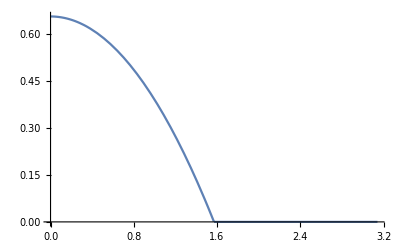

```mathematica
M= 1/(√(π^5/8+2*π^3-24*π^2+48π))
f[θ_,ϕ_]:= Piecewise[{{M*(π^2/4-θ^2),0<θ<π/2},{0,π/2<θ<π}}]
Plot[f[θ,0],{θ,0,Pi}]
```

(a) find the |0,0⟩, |1,-1⟩, |1,0⟩, |1,1⟩ terms in the spherical harmonic expansion of f(θ,ϕ) 

We will first calculate the coefficients by performing the inner products ⟨ l,m | f(θ,ϕ) ⟩ which turn into double integrals over the surface of the sphere.

```mathematica
Subscript[C, 0,0]= Integrate[Conjugate[SphericalHarmonicY[0,0,θ,ϕ]]*f[θ,ϕ]*Sin[θ],{θ,0,π},{ϕ,0,2*π}]
Subscript[C, 1,-1]= Integrate[Conjugate[SphericalHarmonicY[1,-1,θ,ϕ]]*f[θ,ϕ]*Sin[θ],{θ,0,π},{ϕ,0,2*π}]
Subscript[C, 1,0]= Integrate[Conjugate[SphericalHarmonicY[1,0,θ,ϕ]]*f[θ,ϕ]*Sin[θ],{θ,0,π},{ϕ,0,2*π}]
Subscript[C, 1,1]= Integrate[Conjugate[SphericalHarmonicY[1,1,θ,ϕ]]*f[θ,ϕ]*Sin[θ],{θ,0,π},{ϕ,0,2*π}]
```

```mathematica
Y1[θ_,ϕ_]= Subscript[C, 0,0]*SphericalHarmonicY[0,0,θ,ϕ]
```

(8-4 π+π^2)/(2 √(2 π (384-192 π+16 π^2+π^4)))

```mathematica
Y2[θ_,ϕ_]=Subscript[C, 1,-1]*SphericalHarmonicY[1,-1,θ,ϕ]
```

0

```mathematica
Y3[θ_,ϕ_]= Subscript[C, 1,0]*SphericalHarmonicY[1,0,θ,ϕ]
```

(3 (4+π^2) Cos[θ])/(8 √(2 π (384-192 π+16 π^2+π^4)))

```mathematica
Y4[θ_,ϕ_]= Subscript[C, 1,1]*SphericalHarmonicY[1,1,θ,ϕ]
```

0

(b) If in the state above, what is the probability that a measurement of L^2 is 2 ℏ^2 or 4ℏ^2?    We know that 4 ℏ^2 is impossible because the energy is given as ℏ^2 ℓ(ℓ+1) where ℓ must be a positive integer and so there is no way to make 4=ℓ(ℓ+1). 

P(L^2= 2 ℏ^2) = |C_(1,-1)|^2+|C_(1,0)|^2+|C_(1,1)|^2 which is calculated below:

```mathematica
Norm[Subscript[C, 1,-1]]^2+Norm[Subscript[C, 1,0]]^2+Norm[Subscript[C, 1,1]]^2
```

(3 (4+π^2)^2)/(32 (384-192 π+16 π^2+π^4))

```mathematica
(3 (4+π^2)^2)/(32 (384-192 π+16 π^2+π^4))//N
```

0.499054

(c) If in the state above, what is the probability that the particle can be found in the region 0<θ<π/6and 0<ϕ<π/6, repeat for (5π)/6<θ<π and (5π)/6<ϕ<π?

For notation we will label the first interval a and the second interval b.

```mathematica
Subscript[P, a]=Integrate[Conjugate[f[θ,ϕ]]*f[θ,ϕ]*Sin[θ], {θ,0,π/6},{ϕ,0,π/6}]//N 
Subscript[P, b]=Integrate[Conjugate[f[θ,ϕ]]*f[θ,ϕ]*Sin[θ], {θ,(5π)/6,π},{ϕ,0,π/6}]//N
```

0.0268989

0.

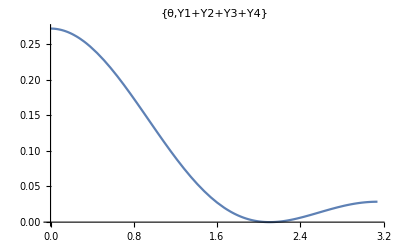

```mathematica
Plot[(Y1[θ,0]+Y2[θ,0]+Y3[θ,0]+Y4[θ,0])^2, {θ,0,π}, PlotLabel->{"θ","Y1+Y2+Y3+Y4"}]
```

This graph as well as the graph from part a do suggest that there will be zero probability in the second region as we can see f is zero there and our approximation is nearly zero over this small interval.